## Mathematica implementation of the simple NN that classifies bundle stability (cf.Section 2.1)

Optional : Seed the random number generator for reproducibility

```mathematica
seed=0;
SeedRandom[seed];
```

### Read in the full data set

```mathematica
hnd=OpenRead[FileNameJoin[{NotebookDirectory[],"../stability_data.txt"}]];
inputStr=ReadString[hnd];
Close[hnd];

(* Convert to array *)
allData=ToExpression[StringReplace[inputStr,{"["->"{","]"->"}"}]];
allData=Table[allData[[i,1]]->{allData[[i,2]]},{i,Length[allData]}];
```

### Perform a train:test split

```mathematica
(* helper function to create random batches *)
shuffleTrainset[trainSet_]:=Module[{},(Return[RandomSample[trainSet]])];

(* shuffle the entire data set once to get random train and test pairs *)
allData=RandomSample[allData];

(* perform a train:test split of 80:20 *)
splitPoint=Ceiling[Length[allData]*0.8];
trainSet=allData[[1;;splitPoint]];
testSet=allData[[splitPoint+1;;]];
```

### Define the NN hyperparameters

```mathematica
(* number of nodes in each layer *)
inputDim=2;
hidden1Dim=4;
hidden2Dim=4;
outputDim=1;

(* set training variables *)
epochs=101;
batchSize=32;
learningRate=0.1;
```

### Set up the NN

```mathematica
nn=NetChain[{hidden1Dim,LogisticSigmoid,hidden2Dim,LogisticSigmoid,1,LogisticSigmoid},"Input"->inputDim,"Output"->outputDim]
```

NetChain[<>]

### Initialize the network

```mathematica
nn=NetInitialize[nn];
```

### Train the NN

```mathematica
(* ADAM Optimizer, Binary cross entropy loss *)
results=NetTrain[nn,trainSet,All,BatchSize->batchSize,LossFunction->CrossEntropyLossLayer["Binary"],MaxTrainingRounds->epochs,
 Method->{"ADAM","LearningRate"->learningRate}];
nn=results["TrainedNet"];
```

### Plot the loss during training

```mathematica
results
```

NetTrainResultsObject[<>]

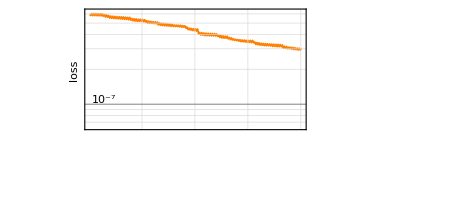

```mathematica
exampleLoss=results["LossEvolutionPlot"]
Export[FileNameJoin[{NotebookDirectory[],"example_loss.pdf"}],exampleLoss];
```

### Evaluate the NN

```mathematica
testSetX=Table[testSet[[i,1]],{i,Length[testSet]}];
testSetY=Table[testSet[[i,2]],{i,Length[testSet]}];
pred=nn[testSetX];

acc=0;
For[i=1,i≤Length[testSetY],i++,
If[Round[pred[[i]]]==testSetY[[i]],acc++];
];
Print["Validation Accuracy: ",acc/Length[testSetY]]

evaluationResult={{"x","y","yhat"}};
For[i=1,i≤Length[testSetY],i++,
AppendTo[evaluationResult,{testSetX[[i]],testSetY[[i,1]],Round[pred[[i,1]]]}];
];
Print[MatrixForm[evaluationResult]];
Print["Evaluation complete!"]
```

Validation Accuracy: 1

(x | y | yhat
{-3,-5} | 0 | 0
{-8,4} | 1 | 1
{-5,-10} | 0 | 0
{9,-8} | 1 | 1
{-1,4} | 1 | 1
{10,-9} | 1 | 1
{-8,2} | 1 | 1
{9,-9} | 1 | 1
{-7,6} | 1 | 1
{7,9} | 0 | 0
{-9,4} | 1 | 1
{-6,8} | 1 | 1
{6,1} | 0 | 0
{7,-5} | 1 | 1
{5,0} | 1 | 1
{4,-8} | 1 | 1
{-10,3} | 1 | 1
{-6,6} | 1 | 1
{-2,10} | 1 | 1
{-4,7} | 1 | 1
{-9,6} | 1 | 1
{-4,5} | 1 | 1
{-8,0} | 1 | 1
{7,1} | 0 | 0
{-7,-8} | 0 | 0
{10,2} | 0 | 0
{8,-3} | 1 | 1
{-2,9} | 1 | 1
{-1,7} | 1 | 1
{-6,9} | 1 | 1
{-10,-4} | 0 | 0
{4,-5} | 1 | 1
{10,9} | 0 | 0
{6,7} | 0 | 0
{1,-3} | 1 | 1
{8,-2} | 1 | 1
{8,4} | 0 | 0
{0,8} | 1 | 1
{6,6} | 0 | 0
{-4,8} | 1 | 1
{8,10} | 0 | 0
{0,-2} | 1 | 1
{3,-4} | 1 | 1
{9,-4} | 1 | 1
{8,8} | 0 | 0
{-9,-10} | 0 | 0
{-3,-10} | 0 | 0
{2,-3} | 1 | 1
{-3,10} | 1 | 1
{-4,3} | 1 | 1
{8,9} | 0 | 0
{-10,-8} | 0 | 0
{3,7} | 0 | 0
{9,3} | 0 | 0
{-7,0} | 1 | 1
{-2,-3} | 0 | 0
{7,2} | 0 | 0
{-2,-8} | 0 | 0
{-6,-10} | 0 | 0
{-10,6} | 1 | 1
{-7,-4} | 0 | 0
{10,10} | 0 | 0
{-9,7} | 1 | 1
{-6,-6} | 0 | 0
{9,1} | 0 | 0
{-3,-9} | 0 | 0
{7,-3} | 1 | 1
{3,2} | 0 | 0
{4,-9} | 1 | 1
{-3,8} | 1 | 1
{-8,-5} | 0 | 0
{2,0} | 1 | 1
{3,0} | 1 | 1
{3,10} | 0 | 0
{-1,1} | 1 | 1
{4,3} | 0 | 0
{5,-2} | 1 | 1
{3,-3} | 1 | 1
{0,3} | 1 | 1
{-2,2} | 1 | 1
{5,6} | 0 | 0
{0,-9} | 1 | 1
{9,7} | 0 | 0
{-8,9} | 1 | 1
{1,-5} | 1 | 1
{4,8} | 0 | 0
{3,9} | 0 | 0
{8,1} | 0 | 0)

Evaluation complete!

### Plot prediction of NN on all data

```mathematica
pred=nn[Table[allData[[i,1]],{i,Length[allData]}]];
allPoints=Table[Flatten[{allData[[i,1]],pred[[i]]}],{i,Length[pred]}];
exampleFunction=ListPointPlot3D[allPoints]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"example_function.pdf"}],exampleFunction];
```